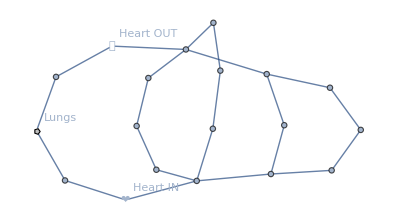

```mathematica
g=Graph[{1<->2,2<->3,3<->4,4<->8,1<->5,5<->6,6<->7,7<->8,1<->14,14<->15,15<->16,16<->8,14<->17,17<->18,18<->19,19<->16,1<->9,9<->10,10<->11,11<->12,12<->13,13<->8},
VertexShape->{9->❤,13->⛲,11->-Graphics-},
VertexLabels->{9->"Heart IN",13->"Heart OUT",11->"Lungs"}
];
g
```

```mathematica
Clear[idx,data]
idx[g_]:=With[{v=VertexList[g]},Association@Table[v[[i]]->i,{i,Length@v}]]
data[graph_]:=<|
g->graph,
v->VertexList[graph],
e->EdgeList[graph],
nv->Length@VertexList[graph],
vi->idx[graph]
|>
```

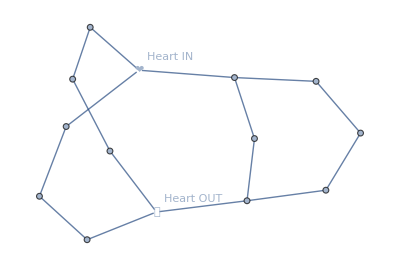
<|g→-Graphics-,v→{1,2,3,4,8,5,6,7,14,15,16,17,18,19},e→{1<->2,2<->3,3<->4,4<->8,1<->5,5<->6,6<->7,7<->8,1<->14,14<->15,15<->16,16<->8,14<->17,17<->18,18<->19,19<->16},nv→14,vi→<|1→1,2→2,3→3,4→4,8→5,5→6,6→7,7→8,14→9,15→10,16→11,17→12,18→13,19→14|>|>

```mathematica
u=data[Graph[{1<->2,2<->3,3<->4,4<->8,1<->5,5<->6,6<->7,7<->8,1<->14,14<->15,15<->16,16<->8,14<->17,17<->18,18<->19,19<->16},
VertexShape->{1->❤,8->⛲},
VertexLabels->{1->"Heart IN",8->"Heart OUT"}
]]
```

```mathematica
Clear[nodePressure,flowRate,eflow,vflow]
nodePressureLin[q_,q0_]:=q/q0-1
nodePressure[q_,q0_]:=With[{L0=1,E=1000,τ0=0.0005},With[{r0=√(q0/(π L0)),r=√(q/(π L0))},
E τ0 (r0(r-r0))/r^3
]]
flowRate[p_,i_,j_]:=p[[j]]-p[[i]]
eflow[g_,p_]:=With[{i=g[vi]},Table[flowRate[p,i[e[[1]]],i[e[[2]]]],{e,g[e]}]]
vflow[g_,ef_]:=With[{v=g[v],e=g[e]},Table[Sum[
Piecewise[{
{ef[[j]],e[[j]][[1]]==v[[i]]},
{-ef[[j]],e[[j]][[2]]==v[[i]]}
},0]
,{j,Length@e}],{i,g[nv]}]]
```

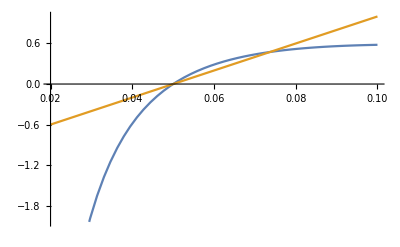

```mathematica
Plot[{
nodePressure[q,0.05],
nodePressureLin[q,0.05]
},{q,0.02,0.10}]
```

```mathematica
qref=ConstantArray[1,u[nv]]
q0=qref+UnitVector[u[nv],1]
nodePressure[q0,qref]
eflow[u,%]
vflow[u,%]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{2,1,1,1,1,1,1,1,1,1,1,1,1,1}

{0.129785,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{-0.129785,0.,0.,0.,-0.129785,0.,0.,0.,-0.129785,0.,0.,0.,0.,0.,0.,0.}

{-0.389355,0.129785,0.,0.,0.,0.129785,0.,0.,0.129785,0.,0.,0.,0.,0.}

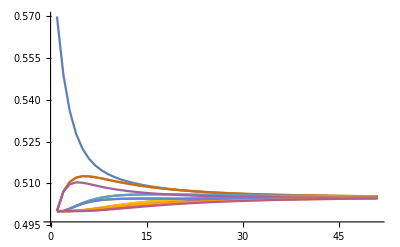

```mathematica
Clear[solve]
solveStep[g_,q0_,qref_,dt_]:=Module[{p,ef,vf},
p=nodePressure[q0,qref];
ef=eflow[g,p];
vf=vflow[g,ef];
q0+dt vf
]
solve[g_,q0_,qref_,dt_]:=Module[{q,p,ef,vf},
q=q0;
For[i=1,i<=10,i++,
p=nodePressure[q,qref];
ef=eflow[g,p];
vf=vflow[g,ef];
q=q+dt vf;
];
q
]
qref=ConstantArray[0.5,u[nv]];
q0=qref+0.07UnitVector[u[nv],1];
qsol=NestList[solveStep[u,#,qref,0.10]&,q0,50];
ListPlot[Transpose@qsol,Joined->True,PlotRange->All]
```

```mathematica
Manipulate[
GraphPlot[u[g],VertexShapeFunction->"Circle",
VertexSize->Table[u[v][[i]]->qsol[[k,i]],{i,Length@u[v]}]],
{k,1,Length@qsol,1}
]
```

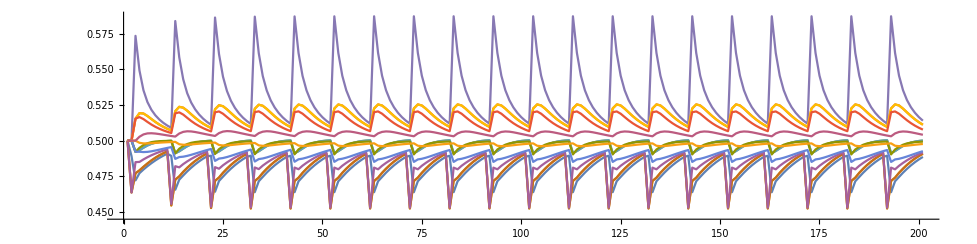

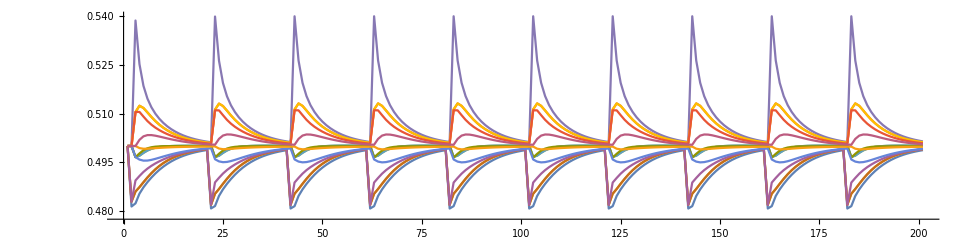

```mathematica
Clear[heartbeat]
heartbeat[g_,q0_,qref_,dt_,hin_,hout_,hvol_,hn_]:=Module[{q1,q2,qm,k},
q1=q0-hvol UnitVector[g[nv],hin];
q1=solveStep[g,q1,qref,dt];
q2=q1+hvol UnitVector[g[nv],hout];
q2=solveStep[g,q2,qref,dt];
qm=NestList[solveStep[g,#,qref,dt]&,q2,hn];
Join[{q1},qm]
]
q0=ConstantArray[1,u[nv]]7./u[nv];
sfast=Flatten[NestList[heartbeat[u,Last[#],q0,0.15,1,5,0.12,8]&,{q0},20],1];
ListPlot[Transpose@%,Joined->True,PlotRange->All,AspectRatio->1/4]
slow=Flatten[NestList[heartbeat[u,Last[#],q0,0.15,1,5,0.07,18]&,{q0},10],1];
ListPlot[Transpose@%,Joined->True,PlotRange->All,AspectRatio->1/4]
```

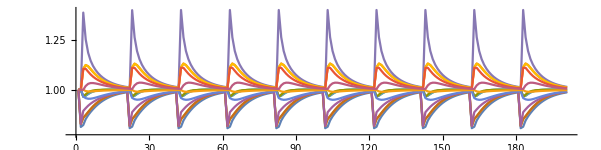

```mathematica
qvis=(#/qref&/@slow-1)5+1;
ListPlot[Transpose@qvis,Joined->True,PlotRange->All,AspectRatio->1/4]
Manipulate[
GraphPlot[u[g],VertexShapeFunction->"Circle",
VertexSize->Table[u[v][[i]]->qvis[[k,i]],{i,Length@u[v]}]],
{k,1,Length@qsol,1}
]
```